# Valore di soglia a_max

```mathematica
Ystud[t_, Ydag_, beta_]:= Ydag * (1- Exp[-beta t])
```

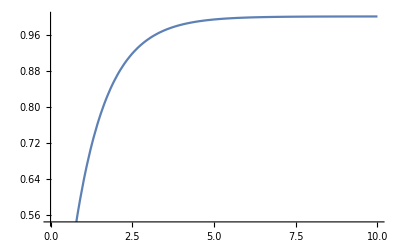

```mathematica
Plot[Ystud[t, 1, 1],{t, 0, 10}]
```

```mathematica
Integrate[Exp[-beta1 t]*((Ystud[t, Ydag, beta]-Ystar)^2 / 2  + amax^2),{t, 0, T}]
```

1/2 (Ydag^2/(2 beta+beta1)-(ⅇ^(-(2 beta+beta1) T) Ydag^2)/(2 beta+beta1)+(2 amax^2+(Ydag-Ystar)^2)/beta1-(ⅇ^(-beta1 T) (2 amax^2+(Ydag-Ystar)^2))/beta1-(2 Ydag (Ydag-Ystar))/(beta+beta1)+(2 ⅇ^(-(beta+beta1) T) Ydag (Ydag-Ystar))/(beta+beta1))

```mathematica
F[Ydag_, Ystar_, beta_, beta1_, amax_, T_]:=1/2 (Ydag^2/(2 beta+beta1)-(ⅇ^(-(2 beta+beta1) T) Ydag^2)/(2 beta+beta1)+(2 amax^2+(Ydag-Ystar)^2)/beta1-(ⅇ^(-beta1 T) (2 amax^2+(Ydag-Ystar)^2))/beta1-(2 Ydag (Ydag-Ystar))/(beta+beta1)+(2 ⅇ^(-(beta+beta1) T) Ydag (Ydag-Ystar))/(beta+beta1))
```

```mathematica
Famax[amax_, Ystar_,Yteach_,  beta_, beta1_, T_]:= F[Yteach * (1-amax) + amax*Ystar, Ystar, beta, beta1, amax, T]
```

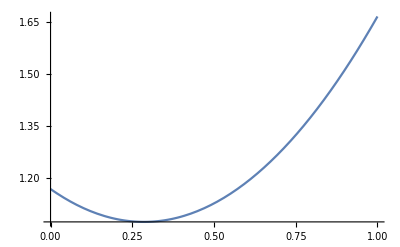

```mathematica
Plot[Famax[amax,2,1,1,1, 100], {amax, 0, 1}]
```

```mathematica
Solve[D[Famax[amax,2,1,1,1, T], amax]==0, amax]
```

{{amax→((-1+ⅇ^T) (1+2 ⅇ^T))/(1-2 ⅇ^T+7 ⅇ^(2 T))}}